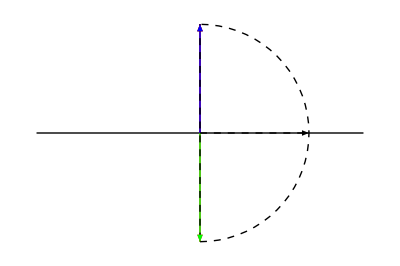

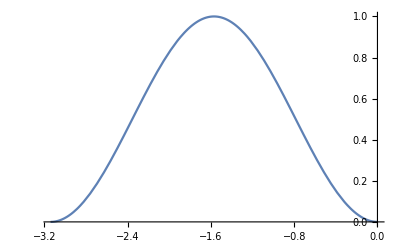

1.5708

```mathematica
vdir={0,1,0};
vnormangle=-90 Degree;
vnorm={Cos[vnormangle+Pi/2],Sin[vnormangle+Pi/2],0};

n=ArcCos[vdir.vnorm];
h1=-180 Degree;
h2=0Degree;

test = ArcCos[{1,0,0}.vnorm]-Pi/2;
 
h1c=test+Max[h1-test,-Pi/2];
h2c=test+Min[h2-test,Pi/2];

base1=Line[{{-1.5,0},{1.5,0}}];
vdir=Arrow[{{0,0},{0,1}}];
norm=Arrow[{{0,0},{vnorm[[1]],vnorm[[2]]}}];

horizon1=Arrow[{{0,0},{Cos[h1+Pi/2],Sin[h1+Pi/2]}}];
horizon2=Arrow[{{0,0},{Cos[h2+Pi/2],Sin[h2+Pi/2]}}];
horizon1c=Arrow[{{0,0},{Cos[h1c+Pi/2],Sin[h1c+Pi/2]}}];
horizon2c=Arrow[{{0,0},{Cos[h2c+Pi/2],Sin[h2c+Pi/2]}}];

halfcircle=Circle[{0,0},1,{vnormangle,Pi+vnormangle}];
base2=Line[{{-Cos[vnormangle],-Sin[vnormangle]},{Cos[vnormangle],Sin[vnormangle]}}];

Graphics[{base1,vdir,Red,horizon1,horizon2,Green,horizon1c,Blue,horizon2c,Black,Dashed,base2,halfcircle,norm}]
Plot[Cos[x-test]*Abs[Sin[x]],{x,h1c,h2c}]

f[gamma_,t1_,t2_] :=Integrate[Cos[x-gamma]*Abs[Sin[x]],{x,t1,t2},Assumptions->(0<t2<Pi)&&(-Pi<t1<0)]
N[f[test,h1c,h2c]]
```